```mathematica
names={"11_K_m9_3200_t420.txt","11b_K_m9_3200_t420.txt","13_K_m8_3200_t420.txt","15_K_m7_3200_t420.txt","17_K_m6_3200_t420.txt","19_K_m5_3200_t480.txt","21_K_m4_3200_t480.txt","23_K_m3_3200_t540.txt","25_K_m2_3200_t540.txt","27_K_m1_3200_t660.txt","29_K_m0_3200_t780.txt"};
imp=Table[Import[ParentDirectory[NotebookDirectory[]]<>"\\data\\"<>names[[i]],"Table",NumberPoint->","],{i,1,Length[names]}]
```

{{{3200.,6.186}},{{3200.,5.848}},{{3200.,5.952}},{{3200.,6.057}},{{3200.,5.533}},{{3200.,5.721}},{{3200.,5.285}},{{3200.,5.104}},{{3200.,4.563}},{{3200.,4.011}},{{3200.,3.04}}}

```mathematica
m={2,2,1.9,1.7,1.5,1.3,1.1,0.9,0.7,0.5,0.3}
```

{2,2,1.9,1.7,1.5,1.3,1.1,0.9,0.7,0.5,0.3}

```mathematica
data=Transpose[{m,n}]
```

{{2,6.186},{2,5.848},{1.9,5.952},{1.7,6.057},{1.5,5.533},{1.3,5.721},{1.1,5.285},{0.9,5.104},{0.7,4.563},{0.5,4.011},{0.3,3.04}}

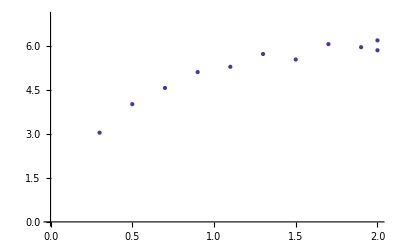

```mathematica
ListPlot[data,PlotRange->{0,7}]
```

```mathematica
nlm=NonlinearModelFit[data,a (1-Exp[-b x]),{a,b},x]
nlm["ParameterTable"]
nlm["CovarianceMatrix"]//MatrixForm
nlm["CorrelationMatrix"]//MatrixForm
{bands90[x_],bands99[x_],bands999[x_]}=Table[nlm["MeanPredictionBands",ConfidenceLevel->cl],{cl,{.9,.99,.999}}];
```

FittedModel[6.03271 (1-ⅇ^(-2.13352 x))]

| Estimate | Standard Error | t-Statistic | P-Value
a | 6.03271 | 0.0900919 | 66.9617 | 1.86581×10^-13
b | 2.13352 | 0.123911 | 17.2182 | 3.38718×10^-8

(0.00811654 | -0.0085834
-0.0085834 | 0.0153539)

(1. | -0.76889
-0.76889 | 1.)

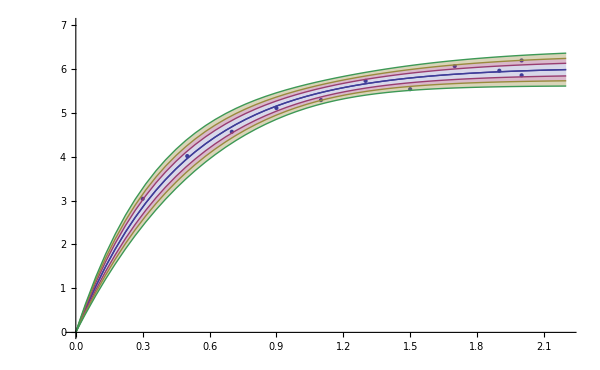

```mathematica
Show[Plot[Normal[nlm],{x,0,2.2},PlotRange->{0,7}],ListPlot[data],Plot[{nlm[x],bands90[x],bands99[x],bands999[x]},{x,0,2.2},Filling->{2->{1},3->{2},4->{3}}],ImageSize->600]
```